```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"];
```

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

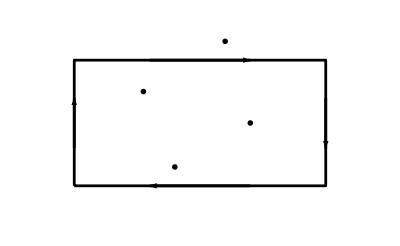

```mathematica
ClearAll[pts,sides,arrowFrac,orientedIntegralFig1]
pts={{0,0},{0,1},{2,1},{2,0},{0,0}};
sides=Partition[pts,2,1];
arrowFrac=0.3;
arrowPaths=Table[Module[{p1=side[[1]],p2=side[[2]],vec,start,end},vec=p2-p1;
start=p1+arrowFrac*vec;
end=p1+(1-arrowFrac)*vec;
{start,end}],{side,sides}];
midpoints=Mean/@sides;
{e1, e2} = IdentityMatrix[2];
latexcolor = "";

orientedIntegralFig1=Graphics[{
Thickness[0.005],
(*Darker[Green],*)
Line[pts],
Arrowheads[0.06],
Arrow/@arrowPaths,

Text[MaTeX[latexcolor <>"\int \mathbf{F}(x_0, y) d\\mathbf{y} \\mathbf{G}(x_0, y)"],( midpoints[[1]]) + 0.55 e1 + 0.25 e2],
Text[MaTeX[latexcolor <>"\int \mathbf{F}(x, y_1) d\\mathbf{x} \\mathbf{G}(x, y_1)"],( midpoints[[2]]) + 0.15 e2 + 0.2 e1],
Text[MaTeX[latexcolor <>"-\int \mathbf{F}(x_1, y) d\\mathbf{y} \\mathbf{G}(x_1, y)"],( midpoints[[3]]) - 0.6  e1],
Text[MaTeX[latexcolor <>"-\int \mathbf{F}(x, y_0) d\\mathbf{x} \\mathbf{G}(x, y_0)"],( midpoints[[4]]) + 0.15 e2 - 0.2 e1]
},
PlotRange->{{-0.3,2.3},{-0.3,1.3}}(*,
GridLines->Automatic*)
]
```

```mathematica
peeters`exportForLatex["orientedIntegralFig1",orientedIntegralFig1]
```

{orientedIntegralFig1.eps,orientedIntegralFig1pn.png}